#### Find the closest path between two elastic maps INSTRUCTIONS: Run common_funs.nb, then ES_FindSymGroups.nb, then this notebook Variables to change: dt, RangeSigma, Tmat (T1, T2)

#### Igel1995

```mathematica
CmatIgel=({{10.0, 3.5, 2.5, -5.0, 0.1, 0.3}, {3.5, 8.0, 1.5, 0.2, -0.1, -0.15}, {2.5, 1.5, 6.0, 1.0, 0.4, 0.24}, {-5.0, 0.2, 1.0, 5.0, 0.35, 0.525}, {0.1, -0.1, 0.4, 0.35, 4.0, -1.0}, {0.3, -0.15, 0.24, 0.525, -1.0, 3.0}});
CmatIgel==Transpose[CmatIgel]
TmatIgel = Simplify[TmatOfCmat[CmatIgel]];
MatrixNote[TmatIgel]="Tmat is TmatIgel";
Print["A given Voigt matrix is ",MatrixForm[CmatIgel]];  
Print["The corresponding [T]_𝔹𝔹 is ",MatrixForm[TmatIgel]];
```

#### Find closest T to ISO

```mathematica
Tmat=TmatIgel;
```

```mathematica
MatrixNote[Tmat]
OutputFor[Tmat,ISO]
```

```mathematica
betaISO =βTinitial[Tmat,ISO]/Degree  (* AngleMatrix[Tmat,Closest[Tmat,ISO]]/Degree *)
TISO =ProjToVSigOfU[Tmat,id,ISO];  (* Closest[Tmat,ISO] *)
MatrixForm[TISO]
```

#### Matrix norms (not used, but worth thinking about)

```mathematica
Ntriv =Norm[Tmat,Frobenius]
Niso =Norm[TISO,Frobenius]
Norm[TISO/Niso,Frobenius]
Norm[Ntriv/Ntriv,Frobenius]
```

#### The angle does not depend on the size of the T

```mathematica
AngleMatrix[Tmat,TISO]/Degree
AngleMatrix[Tmat/Ntriv,TISO/Niso]/Degree
```

#### KEY FUNCTION

```mathematica
TT[t_,Tmat1_,Tmat2_]:=(1-t) Tmat1+t Tmat2
```

#### CHOOSE Tmat1 and Tmat2

```mathematica
Tmat1 =TmatIgel;
Tmat2 =TISO;
MatrixForm[Tmat1]
MatrixForm[TT[0,Tmat1,Tmat2]]
MatrixForm[Tmat2]
MatrixForm[TT[1,Tmat1,Tmat2]]
```

#### t values to use

```mathematica
t1 = -0.1; t2=1;dt =0.05;
t1 = 0; t2=1;dt =0.25;
Ranget=Range[t1,t2,dt]
```

#### Helper function

```mathematica
PrintVoigt[TmatInput_]:=(
Print["A given matrix [T]_𝔹𝔹 is ",MatrixForm[TmatInput] ]; 
Print["The eigenvalues are: ",Eigenvalues[TmatInput] ]; 
Print["The Voigt matrix for the same T is ",MatrixForm[Simplify[CmatOfTmat[TmatInput]]]];)
```

#### Display the set of Tmats as BB and as Voigt

```mathematica
(* MatrixForm[TT[#,Tmat1,Tmat2]]&/@Ranget *)
```

```mathematica
(Print["t = ",# ]; PrintVoigt[TT[#,Tmat1,Tmat2]])&/@Ranget
```

## Preliminaries for beta curves

#### Set of Sigmas to use

```mathematica
RangeSigma={TRIV,MONO,TRIG,ORTH,TET,CUBE,XISO,ISO};
```

```mathematica
RangeSigma={ORTH,TET};
```

#### Example of plotting two sets of points on one plot.

```mathematica
f[t_,Sigma_]:=t/2
```

```mathematica
Graphics[{PointSize[.02],
Table[Point[{t,0}],                    {t,.2,.8,.2}],
Table[Point[{t,f[t,XISO]}],{t,.2,.8,.2}],
Table[Point[{t,f[t,ORTH]}],{t,.2,.8,.2}]},Axes->True,AxesOrigin->{0,0}]
```

#### Example: Closest to MONO for t=0.2

```mathematica
Ttest =TT[.2,Tmat1,Tmat2];
MatrixForm[Ttest]
OutputFor[Ttest,MONO]
```

#### This is the rotation from the minimization.

```mathematica
(* UT[Tmat,Σ] *)
```

#### This is the corresponding elastic map.

```mathematica
(* MatrixForm[ProjToVSigOfU[Tmat,UT[Tmat,Σ],Σ]] *)
```

#### This command is in the common_funs file.

```mathematica
(* Closest[Tmat_,Sigma_]:=ProjToVSigOfU[Tmat,UT[Tmat,Sigma],Sigma]; *)
```

#### This is the angle between Tmat and the closest Sigma map.

```mathematica
(* AngleMatrix[Tmat,Closest[Tmat,Sigma]] *)
```

#### This is the first matrix in OutputFor

```mathematica
MatrixForm[UT[Ttest,MONO]]
```

#### This is the last matrix in OutputFor (Closest[Tmat,Sigma] is defined in common_funs.nb)

```mathematica
MatrixForm[Closest[Ttest,MONO]]
```

#### These are the βs in OutputFor

```mathematica
AngleMatrix[Ttest,Closest[Ttest,MONO]]/Degree
```

#### Angle between Tmat and the closest-Sigma to Tmat

```mathematica
f[Tmat_,Sigma_]:=MakeReal[AngleMatrix[Tmat,Closest[Tmat,Sigma]]/Degree];
```

## Calculate distance to each symmetry class

#### OutputFor performs the key calculations (minimizations)

```mathematica
Table[OutputFor[TT[t,Tmat1,Tmat2],#]&/@RangeSigma,{t,t1,t2,dt}]
```

#### Plot all the beta curves together. (With the Closest maps pre-saved, the plotting should be quick.)

```mathematica
line[Sigma_]:=Line[{#,f[TT[#,Tmat1,Tmat2],Sigma]}&/@Ranget];
```

```mathematica
Graphics[{PointSize[.02],
line/@RangeSigma,
Text[Style[#,13],{t1-.09,f[TT[t1,Tmat1,Tmat2],#]}]&/@RangeSigma},Axes->True,AxesOrigin->{t1,0},AspectRatio->1]
```

#### This fancier version will require having run the full set for RangeSigma

```mathematica
Graphics[{PointSize[.02],
line/@RangeSigma,
(* Line[{#,f[TT[#,Tmat1,Tmat2],ORTH]}&/@Ranget], *)
{ColorData["Rainbow"][0/6],Point[{#,f[TT[#,Tmat1,Tmat2],MONO]}]&/@Ranget},
{ColorData["Rainbow"][1/6],Point[{#,f[TT[#,Tmat1,Tmat2],ORTH]}]&/@Ranget},
{ColorData["Rainbow"][2/6],Point[{#,f[TT[#,Tmat1,Tmat2],  TET]}]&/@Ranget},
{ColorData["Rainbow"][3/6],Point[{#,f[TT[#,Tmat1,Tmat2],TRIG]}]&/@Ranget},
{ColorData["Rainbow"][4/6],Point[{#,f[TT[#,Tmat1,Tmat2],XISO]}]&/@Ranget},
{ColorData["Rainbow"][5/6],Point[{#,f[TT[#,Tmat1,Tmat2],CUBE]}]&/@Ranget},
{ColorData["Rainbow"][6/6],Point[{#,f[TT[#,Tmat1,Tmat2],  ISO]}]&/@Ranget},
Point[{#,0}]&/@Ranget,Point[{1,0}],
Text[Style[#,13],{t1-.09,f[TT[t1,Tmat1,Tmat2],#]}]&/@RangeSigma},Axes->True,AxesOrigin->{t1,0},AspectRatio->1,ImageSize->500]
```

## For reference

#### dt = 0.5, t1 = 0, RangeSigma = {ORTH, TET}

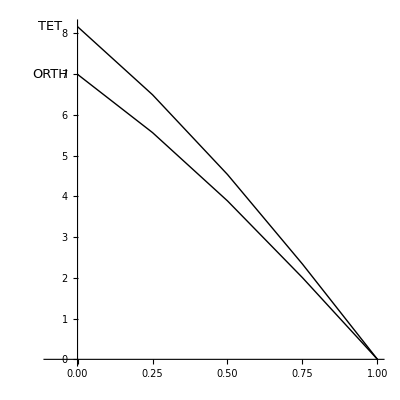

#### dt = 0.1, t1 = 0, RangeSigma = all

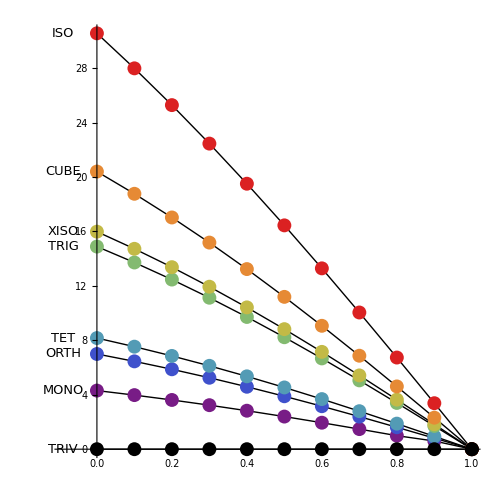

#### dt = 0.05, t1 = -0.1, RangeSigma = all